```mathematica
KnotTheoryPaths={"/Users/scott/projects/KnotTheory/trunk/","/Users/tony/Desktop/"}
$Path=$Path~Join~KnotTheoryPaths;
<<KnotTheory`
```

{/Users/scott/projects/KnotTheory/trunk/,/Users/tony/Desktop/}

Loading KnotTheory` version of January 20, 2015, 10:42:19.1122.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
b[m_,n_,k_]:=BR[k+1,Table[-1,{n}]~Join~Flatten[Table[Range[k],{m}]]]
```

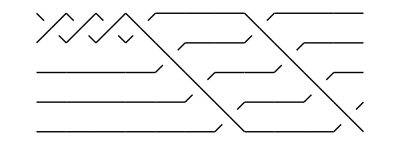

```mathematica
BraidPlot[b[2,3,4]]
```

```mathematica
sInvariant[PD[b[2,8,8]]]
```

0

```mathematica
Table[sInvariant[PD[b[2,n,k]]],{n,1,9,2},{k,1,9,2}]//TableForm
```

0 | 2 | 4 | 6 | 8
0 | 0 | 2 | 4 | 6
-2 | 0 | 0 | 2 | 4
-4 | -2 | 0 | 0 | 2
-6 | -4 | -2 | 0 | 0

```mathematica
Table[sInvariant[PD[b[2,n,k]]],{n,2,10,2},{k,2,10,2}]//TableForm
```

0 | 2 | 4 | 6 | 8
0 | 0 | 2 | 4 | 6
-2 | 0 | 0 | 2 | 4
-4 | -2 | 0 | 0 | 2
-6 | -4 | -2 | 0 | 0

```mathematica
Table[sInvariant[PD[b[3,n,k]]],{n,2,10,2},{k,1,10,3}]//TableForm
```

0 | 6 | 12 | 18
0 | 4 | 10 | 16
-2 | 2 | 8 | 14
-4 | 0 | 6 | 12
-6 | -2 | 4 | 10

```mathematica
Table[sInvariant[PD[b[3,n,k]]],{n,2,16,2},{k,1,7,3}]//TableForm
```

0 | 6 | 12
0 | 4 | 10
-2 | 2 | 8
-4 | 0 | 6
-6 | -2 | 4
-8 | -4 | 2
-10 | -6 | 0
-12 | -8 | -2

```mathematica
Table[sInvariant[PD[b[3,n,k]]],{n,2,20,2},{k,1,4,3}]//TableForm
```

0 | 6
0 | 4
-2 | 2
-4 | 0
-6 | -2
-8 | -4
-10 | -6
-12 | -8
-14 | -10
-16 | -12

```mathematica
Table[sInvariant[PD[b[3,n,k]]],{n,2,10,2},{k,3,10,3}]//TableForm
```

4 | 10 | 16
2 | 8 | 14
0 | 6 | 12
-2 | 4 | 10
-4 | 2 | 8

```mathematica
Table[sInvariant[PD[b[3,n,k]]],{n,2,16,2},{k,3,6,3}]//TableForm
```

4 | 10
2 | 8
0 | 6
-2 | 4
-4 | 2
-6 | 0
-8 | -2
-10 | -4

```mathematica
Table[Length[Skeleton[PD[b[3,n,k]]]],{n,1,10},{k,1,10}]//TableForm
```

2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
1 | 3 | 1 | 1 | 3 | 1 | 1 | 3 | 1 | 1

```mathematica
Table[Length[Skeleton[PD[b[4,n,k]]]],{n,1,10},{k,1,10}]//TableForm
```

1 | 2 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 2
2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1
1 | 2 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 2
2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1
1 | 2 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 2
2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1
1 | 2 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 2
2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1
1 | 2 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 2
2 | 1 | 4 | 1 | 2 | 1 | 4 | 1 | 2 | 1

```mathematica
Table[sInvariant[PD[b[4,n,k]]],{n,1,5,2},{k,1,9,4}]//TableForm
```

2 | 14 | 26
0 | 12 | 24
0 | 10 | 22

```mathematica
Table[sInvariant[PD[b[4,n,k]]],{n,1,9,2},{k,1,5,4}]//TableForm
```

2 | 14
0 | 12
0 | 10
-2 | 8
-4 | 6

```mathematica
Table[sInvariant[PD[b[4,n,k]]],{n,2,5,2},{k,2,9,2}]//TableForm
```

4 | 10 | 16 | 22
2 | 8 | 14 | 20

```mathematica
Table[sInvariant[PD[b[4,n,k]]],{n,2,14,2},{k,2,5,2}]//TableForm
```

4 | 10
2 | 8
0 | 6
-2 | 4
-4 | 2
-6 | 0
-8 | -2